# Laplace Transform Testing

Here, we start by importing utilities that will allow us to use the Loess regression algorithm.

```mathematica
Get[NotebookDirectory[] <> "Loess.m"]
```

Next, we import our encoder velocity data.

```mathematica
Clear[importMotorData, motorData]
importMotorData[] := importMotorData["3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx"];
importMotorData[file_] := Module[{},
Import[NotebookDirectory[]<> file, {"Data", 1}][[1;; ]]
]
motorData = importMotorData[];
```

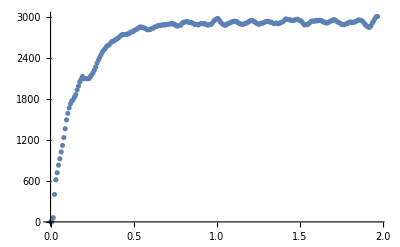

```mathematica
ListPlot[motorData]
```

We now apply Loess to our motor data, then plot the resulting smoothed data and interpolation.

```mathematica
regression=regress[motorData,0.5,2,0];
```

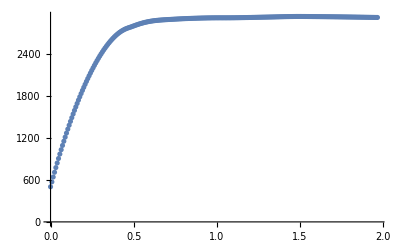

```mathematica
ListPlot[regression,AxesOrigin->{0,0}]
```

InterpolatingFunction[…]

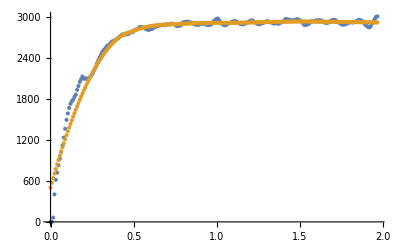

```mathematica
loessInterp = Interpolation[regression, InterpolationOrder-> 3]
ListPlot[{motorData, regression}]
```

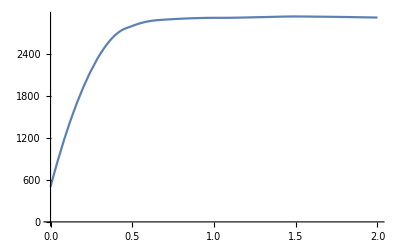

```mathematica
Plot[loessInterp[t],{t,0,2}, AxesOrigin->{0,0}]
```

Loess looks good, but we can’t apply a Laplace transform to an interpolation for some reason.  Instead, we use a (somewhat abstruse) method for creating a piecewise function to fit our motor data.

```mathematica
piecewiseFn=Piecewise[Map[{InterpolatingPolynomial[#,t],t<#[[3,1]]}&,Most[#]],InterpolatingPolynomial[Last@#,t]]&@Partition[motorData,4,1];
```

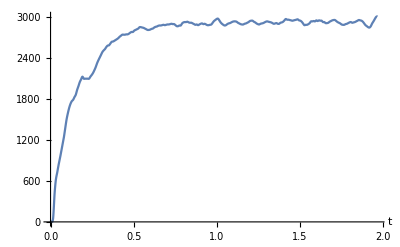

```mathematica
Plot[piecewiseFn,{t,0,1.968},AxesOrigin->{0,0},AxesLabel->Automatic]
```

Now let’s compare the graph above to our original data.

```mathematica
ListPlot[{motorData}]
```

-Graphics-

Success!  They look very similar.  Now that we have an accurate functional representation of our data, let’s take its Laplace transform (this takes a long time right now).

```mathematica
xForm=LaplaceTransform[piecewiseFn,t,s]
```

1/s^4 7.90816×10^-136 ⅇ^(-1.952 s) (-2.46976×10^142-6.1744×10^142 ⅇ^(0.008 s)+1.11139×10^143 ⅇ^(0.016 s)-6.1744×10^142 ⅇ^(0.024 s)-4.93952×10^142 ⅇ^(0.032 s)+1.23488×10^142 ⅇ^(0.04 s)+4.93952×10^142 ⅇ^(0.048 s)-4.93952×10^142 ⅇ^(0.056 s)+2.46976×10^142 ⅇ^(0.072 s)+2.46976×10^142 ⅇ^(0.08 s)-6.1744×10^142 ⅇ^(0.088 s)+7.40928×10^142 ⅇ^(0.096 s)-3.70464×10^142 ⅇ^(0.104 s)+1.23488×10^142 ⅇ^(0.112 s)-2.46976×10^142 ⅇ^(0.12 s)+4.93952×10^142 ⅇ^(0.128 s)-1.11139×10^143 ⅇ^(0.136 s)+9.87904×10^142 ⅇ^(0.144 s)-1.23488×10^142 ⅇ^(0.152 s)-3.70464×10^142 ⅇ^(0.168 s)+6.1744×10^142 ⅇ^(0.176 s)-4.93952×10^142 ⅇ^(0.184 s)+2.46976×10^142 ⅇ^(0.192 s)-4.93952×10^142 ⅇ^(0.2 s)+4.93952×10^142 ⅇ^(0.208 s)-2.46976×10^142 ⅇ^(0.224 s)-2.46976×10^142 ⅇ^(0.232 s)+6.1744×10^142 ⅇ^(0.24 s)-2.46976×10^142 ⅇ^(0.248 s)+1.23488×10^142 ⅇ^(0.256 s)-2.46976×10^142 ⅇ^(0.264 s)+4.93952×10^142 ⅇ^(0.272 s)-4.93952×10^142 ⅇ^(0.28 s)+3.70464×10^142 ⅇ^(0.288 s)-9.87904×10^142 ⅇ^(0.296 s)+1.60534×10^143 ⅇ^(0.304 s)-1.85232×10^143 ⅇ^(0.312 s)+1.60534×10^143 ⅇ^(0.32 s)-1.11139×10^143 ⅇ^(0.328 s)+1.35837×10^143 ⅇ^(0.336 s)-1.97581×10^143 ⅇ^(0.344 s)+2.22278×10^143 ⅇ^(0.352 s)-1.85232×10^143 ⅇ^(0.36 s)+1.11139×10^143 ⅇ^(0.368 s)-1.11139×10^143 ⅇ^(0.376 s)+1.60534×10^143 ⅇ^(0.384 s)-9.87904×10^142 ⅇ^(0.392 s)+2.46976×10^142 ⅇ^(0.4 s)-4.93952×10^142 ⅇ^(0.408 s)+1.23488×10^143 ⅇ^(0.416 s)-1.60534×10^143 ⅇ^(0.424 s)+4.93952×10^142 ⅇ^(0.432 s)+2.46976×10^142 ⅇ^(0.44 s)+4.93952×10^142 ⅇ^(0.448 s)-1.23488×10^143 ⅇ^(0.456 s)+1.23488×10^143 ⅇ^(0.464 s)-4.93952×10^142 ⅇ^(0.472 s)+2.46976×10^142 ⅇ^(0.488 s)-4.93952×10^142 ⅇ^(0.496 s)+2.46976×10^142 ⅇ^(0.504 s)-1.23488×10^142 ⅇ^(0.512 s)+4.93952×10^142 ⅇ^(0.52 s)-1.35837×10^143 ⅇ^(0.528 s)+1.72883×10^143 ⅇ^(0.536 s)-4.93952×10^142 ⅇ^(0.544 s)-3.70464×10^142 ⅇ^(0.552 s)-2.46976×10^142 ⅇ^(0.56 s)+9.87904×10^142 ⅇ^(0.568 s)-7.40928×10^142 ⅇ^(0.576 s)-4.93952×10^142 ⅇ^(0.584 s)+9.87904×10^142 ⅇ^(0.592 s)-7.40928×10^142 ⅇ^(0.608 s)+2.46976×10^142 ⅇ^(0.616 s)+2.46976×10^142 ⅇ^(0.624 s)-1.23488×10^142 ⅇ^(0.632 s)-2.46976×10^142 ⅇ^(0.64 s)+3.70464×10^142 ⅇ^(0.648 s)-2.46976×10^142 ⅇ^(0.672 s)+6.1744×10^142 ⅇ^(0.688 s)-7.40928×10^142 ⅇ^(0.696 s)+2.46976×10^142 ⅇ^(0.704 s)-2.46976×10^142 ⅇ^(0.712 s)+4.93952×10^142 ⅇ^(0.72 s)-7.40928×10^142 ⅇ^(0.728 s)+7.40928×10^142 ⅇ^(0.736 s)-3.70464×10^142 ⅇ^(0.744 s)+4.93952×10^142 ⅇ^(0.752 s)-4.93952×10^142 ⅇ^(0.76 s)+2.46976×10^142 ⅇ^(0.768 s)-3.70464×10^142 ⅇ^(0.776 s)+6.1744×10^142 ⅇ^(0.784 s)-4.93952×10^142 ⅇ^(0.792 s)+1.23488×10^142 ⅇ^(0.8 s)-1.23488×10^142 ⅇ^(0.808 s)+2.46976×10^142 ⅇ^(0.816 s)-4.93952×10^142 ⅇ^(0.824 s)+4.93952×10^142 ⅇ^(0.832 s)-1.23488×10^142 ⅇ^(0.84 s)+1.23488×10^142 ⅇ^(0.856 s)-3.70464×10^142 ⅇ^(0.872 s)+2.46976×10^142 ⅇ^(0.88 s)+3.70464×10^142 ⅇ^(0.888 s)-2.46976×10^142 ⅇ^(0.896 s)-3.70464×10^142 ⅇ^(0.904 s)+2.46976×10^142 ⅇ^(0.912 s)+1.23488×10^142 ⅇ^(0.92 s)-4.93952×10^142 ⅇ^(0.928 s)-2.46976×10^142 ⅇ^(0.936 s)+1.11139×10^143 ⅇ^(0.944 s)-2.46976×10^142 ⅇ^(0.952 s)-4.93952×10^142 ⅇ^(0.96 s)+4.93952×10^142 ⅇ^(0.968 s)+2.46976×10^142 ⅇ^(0.976 s)-9.87904×10^142 ⅇ^(0.984 s)+6.1744×10^142 ⅇ^(0.992 s)-3.70464×10^142 ⅇ^(1.008 s)-1.23488×10^142 ⅇ^(1.016 s)+1.11139×10^143 ⅇ^(1.024 s)-1.48186×10^143 ⅇ^(1.032 s)+9.87904×10^142 ⅇ^(1.04 s)-1.23488×10^142 ⅇ^(1.048 s)+3.70464×10^142 ⅇ^(1.056 s)-1.35837×10^143 ⅇ^(1.064 s)+1.60534×10^143 ⅇ^(1.072 s)-1.11139×10^143 ⅇ^(1.08 s)+3.70464×10^142 ⅇ^(1.088 s)-2.46976×10^142 ⅇ^(1.096 s)+6.1744×10^142 ⅇ^(1.104 s)-3.70464×10^142 ⅇ^(1.112 s)-4.93952×10^142 ⅇ^(1.12 s)+9.87904×10^142 ⅇ^(1.128 s)-7.40928×10^142 ⅇ^(1.136 s)+1.23488×10^142 ⅇ^(1.144 s)+1.23488×10^143 ⅇ^(1.16 s)-2.0993×10^143 ⅇ^(1.168 s)+1.48186×10^143 ⅇ^(1.176 s)-3.70464×10^142 ⅇ^(1.184 s)-4.93952×10^142 ⅇ^(1.192 s)+8.64416×10^142 ⅇ^(1.208 s)-8.64416×10^142 ⅇ^(1.216 s)+6.1744×10^142 ⅇ^(1.224 s)-1.23488×10^142 ⅇ^(1.232 s)-3.70464×10^142 ⅇ^(1.24 s)+3.70464×10^142 ⅇ^(1.248 s)+1.23488×10^142 ⅇ^(1.256 s)-7.40928×10^142 ⅇ^(1.264 s)+7.40928×10^142 ⅇ^(1.272 s)-1.23488×10^142 ⅇ^(1.28 s)-3.70464×10^142 ⅇ^(1.288 s)+2.46976×10^142 ⅇ^(1.296 s)+2.46976×10^142 ⅇ^(1.304 s)-4.93952×10^142 ⅇ^(1.312 s)+2.46976×10^142 ⅇ^(1.32 s)+3.70464×10^142 ⅇ^(1.328 s)-7.40928×10^142 ⅇ^(1.336 s)+6.1744×10^142 ⅇ^(1.344 s)-2.46976×10^142 ⅇ^(1.352 s)+1.23488×10^142 ⅇ^(1.36 s)-3.70464×10^142 ⅇ^(1.368 s)+2.46976×10^142 ⅇ^(1.376 s)-1.23488×10^142 ⅇ^(1.384 s)+2.46976×10^142 ⅇ^(1.392 s)-2.46976×10^142 ⅇ^(1.4 s)-2.46976×10^142 ⅇ^(1.408 s)+1.11139×10^143 ⅇ^(1.416 s)-9.87904×10^142 ⅇ^(1.424 s)+2.46976×10^142 ⅇ^(1.432 s)-2.46976×10^142 ⅇ^(1.44 s)+9.87904×10^142 ⅇ^(1.448 s)-1.48186×10^143 ⅇ^(1.456 s)+8.64416×10^142 ⅇ^(1.464 s)+1.23488×10^142 ⅇ^(1.472 s)-1.23488×10^142 ⅇ^(1.48 s)-4.93952×10^142 ⅇ^(1.488 s)+6.1744×10^142 ⅇ^(1.496 s)-3.70464×10^142 ⅇ^(1.504 s)-2.46976×10^142 ⅇ^(1.512 s)+7.40928×10^142 ⅇ^(1.52 s)-4.93952×10^142 ⅇ^(1.528 s)+3.70464×10^142 ⅇ^(1.536 s)-2.46976×10^142 ⅇ^(1.544 s)-2.46976×10^142 ⅇ^(1.552 s)+4.93952×10^142 ⅇ^(1.56 s)-2.46976×10^142 ⅇ^(1.568 s)-6.1744×10^142 ⅇ^(1.576 s)+1.11139×10^143 ⅇ^(1.584 s)-1.35837×10^143 ⅇ^(1.6 s)+9.87904×10^142 ⅇ^(1.608 s)+3.70464×10^142 ⅇ^(1.616 s)-8.64416×10^142 ⅇ^(1.624 s)+1.23488×10^142 ⅇ^(1.632 s)+6.1744×10^142 ⅇ^(1.64 s)-3.70464×10^142 ⅇ^(1.648 s)-1.23488×10^142 ⅇ^(1.656 s)+6.1744×10^142 ⅇ^(1.672 s)-6.1744×10^142 ⅇ^(1.68 s)+2.46976×10^142 ⅇ^(1.688 s)-2.46976×10^142 ⅇ^(1.696 s)-1.23488×10^142 ⅇ^(1.704 s)+1.11139×10^143 ⅇ^(1.712 s)-1.60534×10^143 ⅇ^(1.72 s)+7.40928×10^142 ⅇ^(1.728 s)+7.40928×10^142 ⅇ^(1.744 s)-3.21069×10^143 ⅇ^(1.752 s)+4.19859×10^143 ⅇ^(1.76 s)-2.22278×10^143 ⅇ^(1.768 s)+1.11139×10^143 ⅇ^(1.776 s)-1.11139×10^143 ⅇ^(1.784 s)+1.72883×10^143 ⅇ^(1.792 s)-2.22278×10^143 ⅇ^(1.8 s)+1.60534×10^143 ⅇ^(1.808 s)-1.60534×10^143 ⅇ^(1.816 s)+9.87904×10^142 ⅇ^(1.824 s)+8.1425×10^128 ⅇ^(1.832 s)+1.23488×10^142 ⅇ^(1.84 s)-6.1744×10^142 ⅇ^(1.848 s)+1.35837×10^143 ⅇ^(1.856 s)-4.93952×10^142 ⅇ^(1.864 s)-2.46976×10^142 ⅇ^(1.872 s)-7.40928×10^142 ⅇ^(1.88 s)+8.64416×10^142 ⅇ^(1.888 s)-7.40928×10^142 ⅇ^(1.896 s)+1.04193×10^143 ⅇ^(1.904 s)-3.48167×10^143 ⅇ^(1.912 s)+2.58124×10^143 ⅇ^(1.92 s)+1.03215×10^144 ⅇ^(1.928 s)-1.52859×10^144 ⅇ^(1.936 s)+5.31684×10^143 ⅇ^(1.952 s)-1.08935×10^127 ⅇ^(0.072 s) s-5.44674×10^126 ⅇ^(0.08 s) s+7.18794×10^124 ⅇ^(1.376 s) s+2.73142×10^126 ⅇ^(1.384 s) s-2.33608×10^125 ⅇ^(1.488 s) s+2.33608×10^125 ⅇ^(1.496 s) s+2.72337×10^126 ⅇ^(1.544 s) s+1.36168×10^126 ⅇ^(1.552 s) s-7.72848×10^125 ⅇ^(1.824 s) s+1.25128×10^126 ⅇ^(1.832 s) s+1.39849×10^126 ⅇ^(1.84 s) s-2.00997×10^125 ⅇ^(1.904 s) s-6.65247×10^125 ⅇ^(1.912 s) s+6.02503×10^124 ⅇ^(1.92 s) s+6.70376×10^125 ⅇ^(1.928 s) s+1.22478×10^126 ⅇ^(1.936 s) s-3.01859×10^141 ⅇ^(1.952 s) s+2.63441×10^137 s^2+6.58602×10^137 ⅇ^(0.008 s) s^2-1.18548×10^138 ⅇ^(0.016 s) s^2+6.58602×10^137 ⅇ^(0.024 s) s^2+5.26882×10^137 ⅇ^(0.032 s) s^2-1.3172×10^137 ⅇ^(0.04 s) s^2-5.26882×10^137 ⅇ^(0.048 s) s^2+5.26882×10^137 ⅇ^(0.056 s) s^2-2.63441×10^137 ⅇ^(0.072 s) s^2-2.63441×10^137 ⅇ^(0.08 s) s^2+6.58602×10^137 ⅇ^(0.088 s) s^2-7.90323×10^137 ⅇ^(0.096 s) s^2+3.95161×10^137 ⅇ^(0.104 s) s^2-1.3172×10^137 ⅇ^(0.112 s) s^2+2.63441×10^137 ⅇ^(0.12 s) s^2-5.26882×10^137 ⅇ^(0.128 s) s^2+1.18548×10^138 ⅇ^(0.136 s) s^2-1.05376×10^138 ⅇ^(0.144 s) s^2+1.3172×10^137 ⅇ^(0.152 s) s^2+3.95161×10^137 ⅇ^(0.168 s) s^2-6.58602×10^137 ⅇ^(0.176 s) s^2+5.26882×10^137 ⅇ^(0.184 s) s^2-2.63441×10^137 ⅇ^(0.192 s) s^2+5.26882×10^137 ⅇ^(0.2 s) s^2-5.26882×10^137 ⅇ^(0.208 s) s^2+2.63441×10^137 ⅇ^(0.224 s) s^2+2.63441×10^137 ⅇ^(0.232 s) s^2-6.58602×10^137 ⅇ^(0.24 s) s^2+2.63441×10^137 ⅇ^(0.248 s) s^2-1.3172×10^137 ⅇ^(0.256 s) s^2+2.63441×10^137 ⅇ^(0.264 s) s^2-5.26882×10^137 ⅇ^(0.272 s) s^2+5.26882×10^137 ⅇ^(0.28 s) s^2-3.95161×10^137 ⅇ^(0.288 s) s^2+1.05376×10^138 ⅇ^(0.296 s) s^2-1.71237×10^138 ⅇ^(0.304 s) s^2+1.97581×10^138 ⅇ^(0.312 s) s^2-1.71237×10^138 ⅇ^(0.32 s) s^2+1.18548×10^138 ⅇ^(0.328 s) s^2-1.44893×10^138 ⅇ^(0.336 s) s^2+2.10753×10^138 ⅇ^(0.344 s) s^2-2.37097×10^138 ⅇ^(0.352 s) s^2+1.97581×10^138 ⅇ^(0.36 s) s^2-1.18548×10^138 ⅇ^(0.368 s) s^2+1.18548×10^138 ⅇ^(0.376 s) s^2-1.71237×10^138 ⅇ^(0.384 s) s^2+1.05376×10^138 ⅇ^(0.392 s) s^2-2.63441×10^137 ⅇ^(0.4 s) s^2+5.26882×10^137 ⅇ^(0.408 s) s^2-1.3172×10^138 ⅇ^(0.416 s) s^2+1.71237×10^138 ⅇ^(0.424 s) s^2-5.26882×10^137 ⅇ^(0.432 s) s^2-2.63441×10^137 ⅇ^(0.44 s) s^2-5.26882×10^137 ⅇ^(0.448 s) s^2+1.3172×10^138 ⅇ^(0.456 s) s^2-1.3172×10^138 ⅇ^(0.464 s) s^2+5.26882×10^137 ⅇ^(0.472 s) s^2-2.63441×10^137 ⅇ^(0.488 s) s^2+5.26882×10^137 ⅇ^(0.496 s) s^2-2.63441×10^137 ⅇ^(0.504 s) s^2+1.3172×10^137 ⅇ^(0.512 s) s^2-5.26882×10^137 ⅇ^(0.52 s) s^2+1.44893×10^138 ⅇ^(0.528 s) s^2-1.84409×10^138 ⅇ^(0.536 s) s^2+5.26882×10^137 ⅇ^(0.544 s) s^2+3.95161×10^137 ⅇ^(0.552 s) s^2+2.63441×10^137 ⅇ^(0.56 s) s^2-1.05376×10^138 ⅇ^(0.568 s) s^2+7.90323×10^137 ⅇ^(0.576 s) s^2+5.26882×10^137 ⅇ^(0.584 s) s^2-1.05376×10^138 ⅇ^(0.592 s) s^2+7.90323×10^137 ⅇ^(0.608 s) s^2-2.63441×10^137 ⅇ^(0.616 s) s^2-2.63441×10^137 ⅇ^(0.624 s) s^2+1.3172×10^137 ⅇ^(0.632 s) s^2+2.63441×10^137 ⅇ^(0.64 s) s^2-3.95161×10^137 ⅇ^(0.648 s) s^2+2.63441×10^137 ⅇ^(0.672 s) s^2-6.58602×10^137 ⅇ^(0.688 s) s^2+7.90323×10^137 ⅇ^(0.696 s) s^2-2.63441×10^137 ⅇ^(0.704 s) s^2+2.63441×10^137 ⅇ^(0.712 s) s^2-5.26882×10^137 ⅇ^(0.72 s) s^2+7.90323×10^137 ⅇ^(0.728 s) s^2-7.90323×10^137 ⅇ^(0.736 s) s^2+3.95161×10^137 ⅇ^(0.744 s) s^2-5.26882×10^137 ⅇ^(0.752 s) s^2+5.26882×10^137 ⅇ^(0.76 s) s^2-2.63441×10^137 ⅇ^(0.768 s) s^2+3.95161×10^137 ⅇ^(0.776 s) s^2-6.58602×10^137 ⅇ^(0.784 s) s^2+5.26882×10^137 ⅇ^(0.792 s) s^2-1.3172×10^137 ⅇ^(0.8 s) s^2+1.3172×10^137 ⅇ^(0.808 s) s^2-2.63441×10^137 ⅇ^(0.816 s) s^2+5.26882×10^137 ⅇ^(0.824 s) s^2-5.26882×10^137 ⅇ^(0.832 s) s^2+1.3172×10^137 ⅇ^(0.84 s) s^2-1.3172×10^137 ⅇ^(0.856 s) s^2+3.95161×10^137 ⅇ^(0.872 s) s^2-2.63441×10^137 ⅇ^(0.88 s) s^2-3.95161×10^137 ⅇ^(0.888 s) s^2+2.63441×10^137 ⅇ^(0.896 s) s^2+3.95161×10^137 ⅇ^(0.904 s) s^2-2.63441×10^137 ⅇ^(0.912 s) s^2-1.3172×10^137 ⅇ^(0.92 s) s^2+5.26882×10^137 ⅇ^(0.928 s) s^2+2.63441×10^137 ⅇ^(0.936 s) s^2-1.18548×10^138 ⅇ^(0.944 s) s^2+2.63441×10^137 ⅇ^(0.952 s) s^2+5.26882×10^137 ⅇ^(0.96 s) s^2-5.26882×10^137 ⅇ^(0.968 s) s^2-2.63441×10^137 ⅇ^(0.976 s) s^2+1.05376×10^138 ⅇ^(0.984 s) s^2-6.58602×10^137 ⅇ^(0.992 s) s^2+3.95161×10^137 ⅇ^(1.008 s) s^2+1.3172×10^137 ⅇ^(1.016 s) s^2-1.18548×10^138 ⅇ^(1.024 s) s^2+1.58065×10^138 ⅇ^(1.032 s) s^2-1.05376×10^138 ⅇ^(1.04 s) s^2+1.3172×10^137 ⅇ^(1.048 s) s^2-3.95161×10^137 ⅇ^(1.056 s) s^2+1.44893×10^138 ⅇ^(1.064 s) s^2-1.71237×10^138 ⅇ^(1.072 s) s^2+1.18548×10^138 ⅇ^(1.08 s) s^2-3.95161×10^137 ⅇ^(1.088 s) s^2+2.63441×10^137 ⅇ^(1.096 s) s^2-6.58602×10^137 ⅇ^(1.104 s) s^2+3.95161×10^137 ⅇ^(1.112 s) s^2+5.26882×10^137 ⅇ^(1.12 s) s^2-1.05376×10^138 ⅇ^(1.128 s) s^2+7.90323×10^137 ⅇ^(1.136 s) s^2-1.3172×10^137 ⅇ^(1.144 s) s^2-1.3172×10^138 ⅇ^(1.16 s) s^2+2.23925×10^138 ⅇ^(1.168 s) s^2-1.58065×10^138 ⅇ^(1.176 s) s^2+3.95161×10^137 ⅇ^(1.184 s) s^2+5.26882×10^137 ⅇ^(1.192 s) s^2-9.22043×10^137 ⅇ^(1.208 s) s^2+9.22043×10^137 ⅇ^(1.216 s) s^2-6.58602×10^137 ⅇ^(1.224 s) s^2+1.3172×10^137 ⅇ^(1.232 s) s^2+3.95161×10^137 ⅇ^(1.24 s) s^2-3.95161×10^137 ⅇ^(1.248 s) s^2-1.3172×10^137 ⅇ^(1.256 s) s^2+7.90323×10^137 ⅇ^(1.264 s) s^2-7.90323×10^137 ⅇ^(1.272 s) s^2+1.3172×10^137 ⅇ^(1.28 s) s^2+3.95161×10^137 ⅇ^(1.288 s) s^2-2.63441×10^137 ⅇ^(1.296 s) s^2-2.63441×10^137 ⅇ^(1.304 s) s^2+5.26882×10^137 ⅇ^(1.312 s) s^2-2.63441×10^137 ⅇ^(1.32 s) s^2-3.95161×10^137 ⅇ^(1.328 s) s^2+7.90323×10^137 ⅇ^(1.336 s) s^2-6.58602×10^137 ⅇ^(1.344 s) s^2+2.63441×10^137 ⅇ^(1.352 s) s^2-1.3172×10^137 ⅇ^(1.36 s) s^2+3.95161×10^137 ⅇ^(1.368 s) s^2-2.63441×10^137 ⅇ^(1.376 s) s^2+1.3172×10^137 ⅇ^(1.384 s) s^2-2.63441×10^137 ⅇ^(1.392 s) s^2+2.63441×10^137 ⅇ^(1.4 s) s^2+2.63441×10^137 ⅇ^(1.408 s) s^2-1.18548×10^138 ⅇ^(1.416 s) s^2+1.05376×10^138 ⅇ^(1.424 s) s^2-2.63441×10^137 ⅇ^(1.432 s) s^2+2.63441×10^137 ⅇ^(1.44 s) s^2-1.05376×10^138 ⅇ^(1.448 s) s^2+1.58065×10^138 ⅇ^(1.456 s) s^2-9.22043×10^137 ⅇ^(1.464 s) s^2-1.3172×10^137 ⅇ^(1.472 s) s^2+1.3172×10^137 ⅇ^(1.48 s) s^2+5.26882×10^137 ⅇ^(1.488 s) s^2-6.58602×10^137 ⅇ^(1.496 s) s^2+3.95161×10^137 ⅇ^(1.504 s) s^2+2.63441×10^137 ⅇ^(1.512 s) s^2-7.90323×10^137 ⅇ^(1.52 s) s^2+5.26882×10^137 ⅇ^(1.528 s) s^2-3.95161×10^137 ⅇ^(1.536 s) s^2+2.63441×10^137 ⅇ^(1.544 s) s^2+2.63441×10^137 ⅇ^(1.552 s) s^2-5.26882×10^137 ⅇ^(1.56 s) s^2+2.63441×10^137 ⅇ^(1.568 s) s^2+6.58602×10^137 ⅇ^(1.576 s) s^2-1.18548×10^138 ⅇ^(1.584 s) s^2+1.44893×10^138 ⅇ^(1.6 s) s^2-1.05376×10^138 ⅇ^(1.608 s) s^2-3.95161×10^137 ⅇ^(1.616 s) s^2+9.22043×10^137 ⅇ^(1.624 s) s^2-1.3172×10^137 ⅇ^(1.632 s) s^2-6.58602×10^137 ⅇ^(1.64 s) s^2+3.95161×10^137 ⅇ^(1.648 s) s^2+1.3172×10^137 ⅇ^(1.656 s) s^2-6.58602×10^137 ⅇ^(1.672 s) s^2+6.58602×10^137 ⅇ^(1.68 s) s^2-2.63441×10^137 ⅇ^(1.688 s) s^2+2.63441×10^137 ⅇ^(1.696 s) s^2+1.3172×10^137 ⅇ^(1.704 s) s^2-1.18548×10^138 ⅇ^(1.712 s) s^2+1.71237×10^138 ⅇ^(1.72 s) s^2-7.90323×10^137 ⅇ^(1.728 s) s^2-7.90323×10^137 ⅇ^(1.744 s) s^2+3.42473×10^138 ⅇ^(1.752 s) s^2-4.4785×10^138 ⅇ^(1.76 s) s^2+2.37097×10^138 ⅇ^(1.768 s) s^2-1.18548×10^138 ⅇ^(1.776 s) s^2+1.18548×10^138 ⅇ^(1.784 s) s^2-1.84409×10^138 ⅇ^(1.792 s) s^2+2.37097×10^138 ⅇ^(1.8 s) s^2-1.71237×10^138 ⅇ^(1.808 s) s^2+1.71237×10^138 ⅇ^(1.816 s) s^2-1.05376×10^138 ⅇ^(1.824 s) s^2-8.68534×10^123 ⅇ^(1.832 s) s^2-1.3172×10^137 ⅇ^(1.84 s) s^2+6.58602×10^137 ⅇ^(1.848 s) s^2-1.44893×10^138 ⅇ^(1.856 s) s^2+5.26882×10^137 ⅇ^(1.864 s) s^2+2.63441×10^137 ⅇ^(1.872 s) s^2+7.90323×10^137 ⅇ^(1.88 s) s^2-9.22043×10^137 ⅇ^(1.888 s) s^2+7.90323×10^137 ⅇ^(1.896 s) s^2-1.11139×10^138 ⅇ^(1.904 s) s^2+3.71379×10^138 ⅇ^(1.912 s) s^2-2.75332×10^138 ⅇ^(1.92 s) s^2-1.10096×10^139 ⅇ^(1.928 s) s^2+1.6305×10^139 ⅇ^(1.936 s) s^2+6.40308×10^138 ⅇ^(1.952 s) s^2+3.48591×10^122 ⅇ^(0.072 s) s^3+5.52034×10^121 ⅇ^(1.376 s) s^3-1.15007×10^122 ⅇ^(1.384 s) s^3+1.49509×10^121 ⅇ^(1.488 s) s^3-1.49509×10^121 ⅇ^(1.496 s) s^3-8.71478×10^121 ⅇ^(1.544 s) s^3-4.00409×10^121 ⅇ^(1.832 s) s^3+6.43191×10^120 ⅇ^(1.904 s) s^3+3.97667×10^121 ⅇ^(1.912 s) s^3-3.36103×10^121 ⅇ^(1.92 s) s^3-2.63416×10^121 ⅇ^(1.928 s) s^3-4.63088×10^121 ⅇ^(1.936 s) s^3+5.16761×10^121 ⅇ^(1.952 s) s^3)

```mathematica
xForm//FullSimplify
```

1/s^4 ⅇ^(-1.952 s) (-1.95313×10^7+208.333 s^2+ⅇ^(1.824 s) (7.8125×10^7+(-6.1118×10^-10-833.333 s) s)+ⅇ^(0.08 s) (1.95313×10^7+(-4.30737×10^-9-208.333 s) s)+ⅇ^(1.84 s) (9.76562×10^6+(1.10595×10^-9-104.167 s) s)+ⅇ^(1.76 s) (3.32031×10^8-3541.67 s^2)+ⅇ^(0.352 s) (1.75781×10^8-1875. s^2)+ⅇ^(0.536 s) (1.36719×10^8-1458.33 s^2)+ⅇ^(1.792 s) (1.36719×10^8-1458.33 s^2)+ⅇ^(0.304 s) (1.26953×10^8-1354.17 s^2)+ⅇ^(0.32 s) (1.26953×10^8-1354.17 s^2)+ⅇ^(0.384 s) (1.26953×10^8-1354.17 s^2)+ⅇ^(1.072 s) (1.26953×10^8-1354.17 s^2)+ⅇ^(1.808 s) (1.26953×10^8-1354.17 s^2)+ⅇ^(1.176 s) (1.17188×10^8-1250. s^2)+ⅇ^(0.336 s) (1.07422×10^8-1145.83 s^2)+ⅇ^(1.856 s) (1.07422×10^8-1145.83 s^2)+ⅇ^(0.416 s) (9.76563×10^7-1041.67 s^2)+ⅇ^(0.464 s) (9.76563×10^7-1041.67 s^2)+ⅇ^(1.16 s) (9.76563×10^7-1041.67 s^2)+ⅇ^(0.016 s) (8.78906×10^7-937.5 s^2)+ⅇ^(0.368 s) (8.78906×10^7-937.5 s^2)+ⅇ^(0.944 s) (8.78906×10^7-937.5 s^2)+ⅇ^(1.024 s) (8.78906×10^7-937.5 s^2)+ⅇ^(1.416 s) (8.78906×10^7-937.5 s^2)+ⅇ^(1.584 s) (8.78906×10^7-937.5 s^2)+ⅇ^(1.712 s) (8.78906×10^7-937.5 s^2)+ⅇ^(1.776 s) (8.78906×10^7-937.5 s^2)+ⅇ^(0.144 s) (7.8125×10^7-833.333 s^2)+ⅇ^(0.568 s) (7.8125×10^7-833.333 s^2)+ⅇ^(0.592 s) (7.8125×10^7-833.333 s^2)+ⅇ^(1.04 s) (7.8125×10^7-833.333 s^2)+ⅇ^(1.128 s) (7.8125×10^7-833.333 s^2)+ⅇ^(1.448 s) (7.8125×10^7-833.333 s^2)+ⅇ^(1.608 s) (7.8125×10^7-833.333 s^2)+ⅇ^(1.208 s) (6.83594×10^7-729.167 s^2)+ⅇ^(1.464 s) (6.83594×10^7-729.167 s^2)+ⅇ^(1.888 s) (6.83594×10^7-729.167 s^2)+ⅇ^(0.096 s) (5.85938×10^7-625. s^2)+ⅇ^(0.736 s) (5.85938×10^7-625. s^2)+ⅇ^(1.272 s) (5.85938×10^7-625. s^2)+ⅇ^(1.52 s) (5.85938×10^7-625. s^2)+ⅇ^(1.728 s) (5.85938×10^7-625. s^2)+ⅇ^(1.744 s) (5.85938×10^7-625. s^2)+ⅇ^(0.176 s) (4.88281×10^7-520.833 s^2)+ⅇ^(0.24 s) (4.88281×10^7-520.833 s^2)+ⅇ^(0.688 s) (4.88281×10^7-520.833 s^2)+ⅇ^(0.784 s) (4.88281×10^7-520.833 s^2)+ⅇ^(0.992 s) (4.88281×10^7-520.833 s^2)+ⅇ^(1.104 s) (4.88281×10^7-520.833 s^2)+ⅇ^(1.224 s) (4.88281×10^7-520.833 s^2)+ⅇ^(1.344 s) (4.88281×10^7-520.833 s^2)+ⅇ^(1.64 s) (4.88281×10^7-520.833 s^2)+ⅇ^(1.672 s) (4.88281×10^7-520.833 s^2)+ⅇ^(0.048 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.128 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.208 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.272 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.432 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.448 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.52 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.72 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.752 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.832 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.968 s) (3.90625×10^7-416.667 s^2)+ⅇ^(1.56 s) (3.90625×10^7-416.667 s^2)+ⅇ^(0.288 s) (2.92969×10^7-312.5 s^2)+ⅇ^(0.648 s) (2.92969×10^7-312.5 s^2)+ⅇ^(0.888 s) (2.92969×10^7-312.5 s^2)+ⅇ^(1.056 s) (2.92969×10^7-312.5 s^2)+ⅇ^(1.088 s) (2.92969×10^7-312.5 s^2)+ⅇ^(1.248 s) (2.92969×10^7-312.5 s^2)+ⅇ^(1.328 s) (2.92969×10^7-312.5 s^2)+ⅇ^(1.536 s) (2.92969×10^7-312.5 s^2)+ⅇ^(1.616 s) (2.92969×10^7-312.5 s^2)+ⅇ^(0.192 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.4 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.44 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.488 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.504 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.616 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.624 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.704 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.768 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.816 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.88 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.912 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.976 s) (1.95313×10^7-208.333 s^2)+ⅇ^(1.296 s) (1.95313×10^7-208.333 s^2)+ⅇ^(1.304 s) (1.95313×10^7-208.333 s^2)+ⅇ^(1.32 s) (1.95313×10^7-208.333 s^2)+ⅇ^(1.392 s) (1.95313×10^7-208.333 s^2)+ⅇ^(1.432 s) (1.95313×10^7-208.333 s^2)+ⅇ^(1.688 s) (1.95313×10^7-208.333 s^2)+ⅇ^(0.04 s) (9.76563×10^6-104.167 s^2)+ⅇ^(0.112 s) (9.76563×10^6-104.167 s^2)+ⅇ^(0.256 s) (9.76563×10^6-104.167 s^2)+ⅇ^(0.8 s) (9.76563×10^6-104.167 s^2)+ⅇ^(0.856 s) (9.76563×10^6-104.167 s^2)+ⅇ^(0.92 s) (9.76563×10^6-104.167 s^2)+ⅇ^(1.144 s) (9.76563×10^6-104.167 s^2)+ⅇ^(1.256 s) (9.76563×10^6-104.167 s^2)+ⅇ^(1.36 s) (9.76563×10^6-104.167 s^2)+ⅇ^(1.472 s) (9.76563×10^6-104.167 s^2)+ⅇ^(1.632 s) (9.76563×10^6-104.167 s^2)+ⅇ^(0.152 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(0.512 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(0.632 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(0.808 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(0.84 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(1.016 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(1.048 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(1.232 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(1.28 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(1.48 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(1.656 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(1.704 s) (-9.76563×10^6+104.167 s^2)+ⅇ^(0.12 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.224 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.232 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.248 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.264 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.56 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.64 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.672 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.712 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.896 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.936 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.952 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.096 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.352 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.4 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.408 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.44 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.512 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.568 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.696 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(1.872 s) (-1.95313×10^7+208.333 s^2)+ⅇ^(0.104 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(0.168 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(0.552 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(0.744 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(0.776 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(0.872 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(0.904 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.008 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.112 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.184 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.24 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.288 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.368 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.504 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(1.648 s) (-2.92969×10^7+312.5 s^2)+ⅇ^(0.032 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.056 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.184 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.2 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.28 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.408 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.472 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.496 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.544 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.584 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.76 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.792 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.824 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.928 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.96 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(1.12 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(1.192 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(1.312 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(1.528 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(1.864 s) (-3.90625×10^7+416.667 s^2)+ⅇ^(0.008 s) (-4.88281×10^7+520.833 s^2)+ⅇ^(0.024 s) (-4.88281×10^7+520.833 s^2)+ⅇ^(0.088 s) (-4.88281×10^7+520.833 s^2)+ⅇ^(1.576 s) (-4.88281×10^7+520.833 s^2)+ⅇ^(1.68 s) (-4.88281×10^7+520.833 s^2)+ⅇ^(1.848 s) (-4.88281×10^7+520.833 s^2)+ⅇ^(0.576 s) (-5.85938×10^7+625. s^2)+ⅇ^(0.608 s) (-5.85938×10^7+625. s^2)+ⅇ^(0.696 s) (-5.85938×10^7+625. s^2)+ⅇ^(0.728 s) (-5.85938×10^7+625. s^2)+ⅇ^(1.136 s) (-5.85938×10^7+625. s^2)+ⅇ^(1.264 s) (-5.85938×10^7+625. s^2)+ⅇ^(1.336 s) (-5.85938×10^7+625. s^2)+ⅇ^(1.88 s) (-5.85938×10^7+625. s^2)+ⅇ^(1.896 s) (-5.85938×10^7+625. s^2)+ⅇ^(1.216 s) (-6.83594×10^7+729.167 s^2)+ⅇ^(1.624 s) (-6.83594×10^7+729.167 s^2)+ⅇ^(0.296 s) (-7.8125×10^7+833.333 s^2)+ⅇ^(0.392 s) (-7.8125×10^7+833.333 s^2)+ⅇ^(0.984 s) (-7.8125×10^7+833.333 s^2)+ⅇ^(1.424 s) (-7.8125×10^7+833.333 s^2)+ⅇ^(0.136 s) (-8.78906×10^7+937.5 s^2)+ⅇ^(0.328 s) (-8.78906×10^7+937.5 s^2)+ⅇ^(0.376 s) (-8.78906×10^7+937.5 s^2)+ⅇ^(1.08 s) (-8.78906×10^7+937.5 s^2)+ⅇ^(1.784 s) (-8.78906×10^7+937.5 s^2)+ⅇ^(0.456 s) (-9.76563×10^7+1041.67 s^2)+ⅇ^(0.528 s) (-1.07422×10^8+1145.83 s^2)+ⅇ^(1.064 s) (-1.07422×10^8+1145.83 s^2)+ⅇ^(1.6 s) (-1.07422×10^8+1145.83 s^2)+ⅇ^(1.032 s) (-1.17188×10^8+1250. s^2)+ⅇ^(1.456 s) (-1.17188×10^8+1250. s^2)+ⅇ^(0.424 s) (-1.26953×10^8+1354.17 s^2)+ⅇ^(1.72 s) (-1.26953×10^8+1354.17 s^2)+ⅇ^(1.816 s) (-1.26953×10^8+1354.17 s^2)+ⅇ^(0.312 s) (-1.46484×10^8+1562.5 s^2)+ⅇ^(0.36 s) (-1.46484×10^8+1562.5 s^2)+ⅇ^(0.344 s) (-1.5625×10^8+1666.67 s^2)+ⅇ^(1.168 s) (-1.66016×10^8+1770.83 s^2)+ⅇ^(1.768 s) (-1.75781×10^8+1875. s^2)+ⅇ^(1.8 s) (-1.75781×10^8+1875. s^2)+ⅇ^(1.752 s) (-2.53906×10^8+2708.33 s^2)+ⅇ^(1.552 s) (-1.95313×10^7+s (1.07684×10^-9+208.333 s))+ⅇ^(1.384 s) (-9.76563×10^6+s (2.16005×10^-9+(104.167-9.09495×10^-14 s) s))+ⅇ^(1.544 s) (-1.95312×10^7+s (2.15368×10^-9+(208.333-6.89179×10^-14 s) s))+ⅇ^(1.936 s) (-1.20884×10^9+s (9.68572×10^-10+(12894.2-3.66218×10^-14 s) s))+ⅇ^(1.832 s) (6.43922×10^-7+s (9.8953×10^-10+(-6.8685×10^-12-3.1665×10^-14 s) s))+ⅇ^(1.92 s) (2.04129×10^8+s (4.76469×10^-11+(-2177.37-2.65796×10^-14 s) s))+ⅇ^(1.928 s) (8.16243×10^8+s (5.30144×10^-10+(-8706.6-2.08314×10^-14 s) s))+ⅇ^(1.496 s) (4.88281×10^7+s (1.84741×10^-10+(-520.833-1.18234×10^-14 s) s))+ⅇ^(1.904 s) (8.23975×10^7+s (-1.58952×10^-10+(-878.906+5.08646×10^-15 s) s))+ⅇ^(1.488 s) (-3.90625×10^7+s (-1.84741×10^-10+(416.667+1.18234×10^-14 s) s))+ⅇ^(1.912 s) (-2.75336×10^8+s (-5.26088×10^-10+(2936.92+3.14481×10^-14 s) s))+ⅇ^(1.952 s) (4.20464×10^8+s (-2.38715×10^6+(5063.66+4.08663×10^-14 s) s))+ⅇ^(1.376 s) (1.95313×10^7+s (5.68434×10^-11+(-208.333+4.36557×10^-14 s) s))+ⅇ^(0.072 s) (1.95312×10^7+s (-8.61473×10^-9+(-208.333+2.75671×10^-13 s) s)))

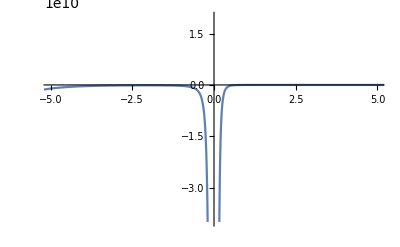

```mathematica
Plot[xForm,{s,-10,10},PlotRange->{{-5,5},{-4*10^10,2*10^10}}]
```